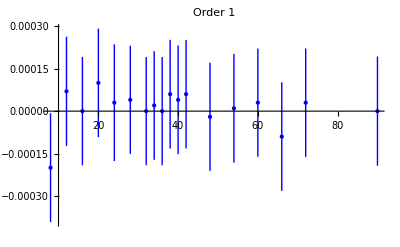

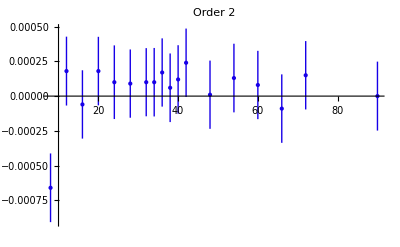

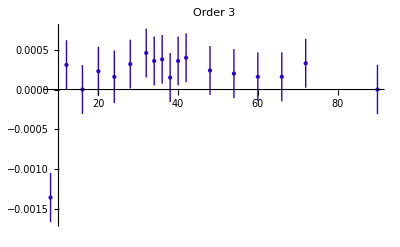

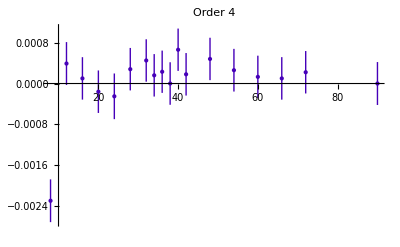

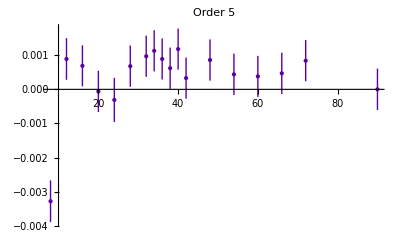

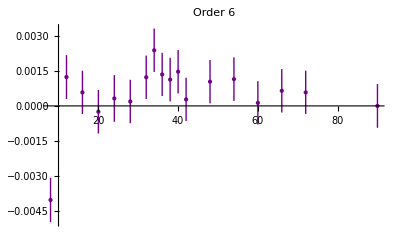

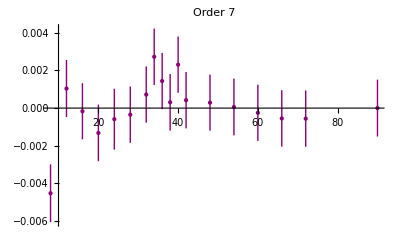

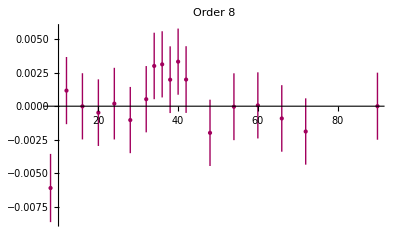

```mathematica
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
LTs=Reverse[{8, 12, 16, 20,24,28,32,34,36,38,40,42,48,54,60,66,72,90}];
Observable="mpnt_";
DataDir="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\";
GrS={};
TData={};
OrderConvergencePlots=Table[{},{io,1,12}];
Do[
Suffix="d2_t"<>ToString[LT]<>"_s108_l3.0120";
RData=Transpose[Import[DataDir<>Observable<>Suffix<>".mean","Table"]];
MeanData=RData[[2]];
ErrData=RData[[3]];
If[LT==90,MeanData0=MeanData;ErrData0=ErrData;];
MeanData=MeanData-MeanData0; 
ErrData=√(ErrData^2+ErrData0^2);
For[io=1,io≤12,io++,
AppendTo[OrderConvergencePlots[[io]],{LT,MeanData[[io]],ErrData[[io]]}];
];
,{LT,LTs}];
For[io=1,io≤12,io++,
r=(io-1)/(12-1);
Gr=PlotWithErrorsTranspose[OrderConvergencePlots[[io]],PlotStyle->{RGBColor[r,0,1-r]},PlotRange->All,PlotLabel->"Order "<>ToString[io]];
Export["G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\mpnt_ltscan_s108_l3.0120_o"<>ToString[io]<>".dat",OrderConvergencePlots[[io]]];
Print[Show[Gr]];
];
```